# MATHEMATICA FOR RESEARCH

## Assignment No:6 Name: Ashtami Bhuleskar Student ID: 18201912 Due Date: 1st November 2018

## BASIC PLOTTING

## Question 1: Create a plot of the three functions x^2-x-1, x^3-2x-2, 2x+1 over the range x∈[-2,2]

```mathematica
Plot[{x^2-x-1,x^3-2*x-2, 2*x+1},{x,-2,2},
PlotTheme->"Marketing", Filling->Axis]
```

-Graphics-

## Question 2: Reproduce the plot from the previous question, but make it so that the background is black, there is a Frame which is styled white, there are no Axes, it has a PlotLabel of “Some interesting functions” and the curves are Orange, LightBlue and Yellow, respectively.

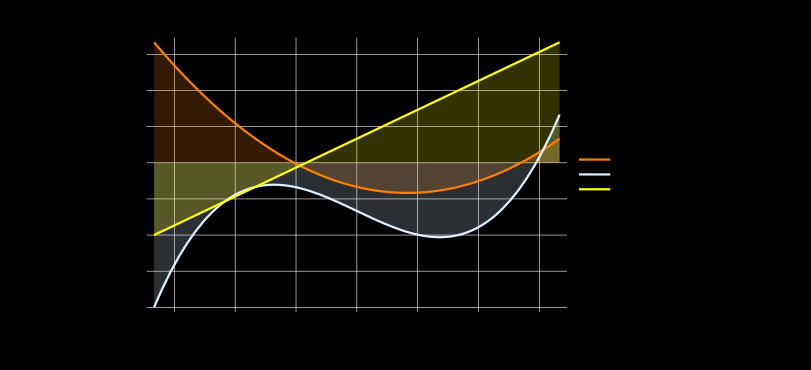

```mathematica
Plot[{x^2-x-1,x^3-2*x-2, 2*x+1},{x,-2,2},
PlotLabel->"Some interesting functions",
PlotTheme-> "Detailed",
Background->Black,
FrameStyle->White,
FrameLabel->{"x","y"},
AxesStyle->None,
PlotStyle->{Directive[Orange],Directive[LightBlue], Directive[Yellow]},
PlotLegends->Placed[LineLegend["Expressions",LegendFunction->(Framed[#,RoundingRadius->5,Background->Gray]&)],{0.85,0.15}],
ImageSize->{600,400},
Filling->Axis]
```

## Question 3: Reproduce the previous plot, but make it so the first curve is solid, the second is Dashed, and the third is Dotted. Hint: Use Directive to set multiply styles for a curve.

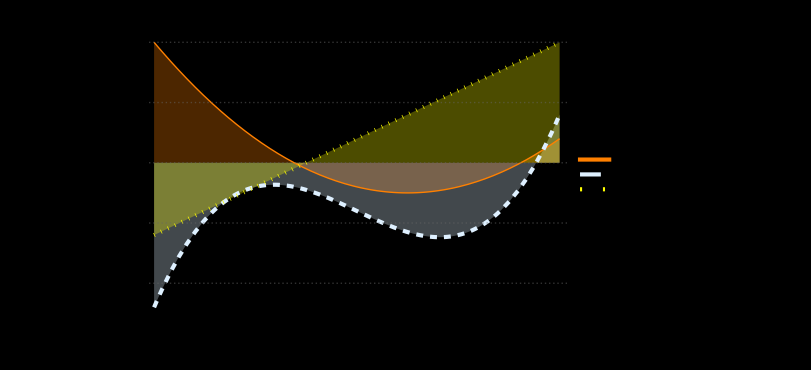

```mathematica
Plot[{x^2-x-1,x^3-2*x-2, 2*x+1},{x,-2,2},
PlotLabel->Style["Some interesting functions"],
PlotTheme-> "Business",
Background->Black,
FrameStyle->White,
FrameLabel->{"x","y"},
AxesStyle->None,
PlotStyle->{Directive[Orange, Thick],Directive[LightBlue, Dashed], Directive[Yellow,Dotted]},
PlotLegends->Placed[LineLegend["Expressions",LegendFunction->(Framed[#,RoundingRadius->5,Background->Gray]&)],{0.85,0.15}],
ImageSize->{600,400},
Filling->Axis]
```

## Question 4: Use Disk and Circle to show display a circle (filled or not filled) centered on x=3, y=2 with radius 4. (Use Show[..., PlotRange→{{-8,8},{-8,8}}] to fix the plot range independently of the parameters of the circle.)

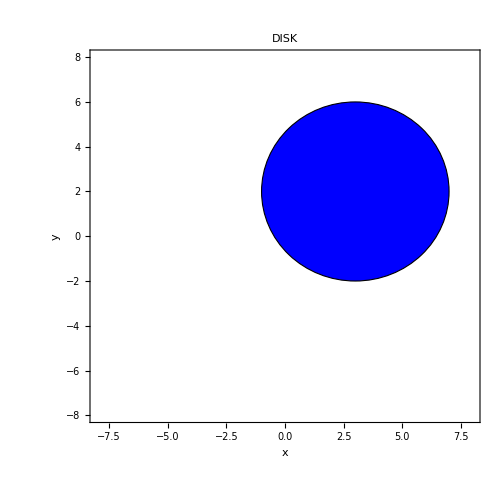

```mathematica
Show[Graphics[ {EdgeForm[Directive[Thick,Dashed,Black]],Blue,Disk[{3,2},4]}],
Frame->True, 
FrameStyle->Directive[Black,Thick],
FrameLabel->{"x","y"}, 
Axes->True ,
PlotTheme -> "Detailed",
PlotLabel->Style["DISK",Black],
PlotRange-> {{-8,8},{-8,8}},
ImageSize->{500,500}]
```

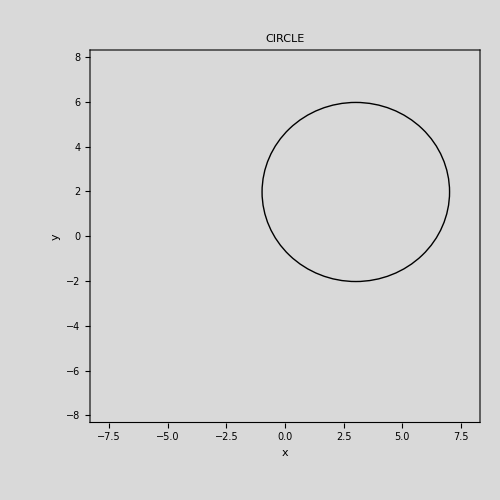

```mathematica
Show[Graphics[Circle[{3,2},4]],
Frame->True,
Background->LightGray,
FrameStyle->Directive[Black,Thick],
FrameLabel->{"x","y"},
Axes->True,
PlotTheme-> "Classic",
PlotLabel->Style["CIRCLE",Black],
PlotRange-> {{-8,8},{-8,8}},
ImageSize->{500,500}]
```

## MANIPULATE:

## Question 5: Create a Manipulate to plot the function a x^3+b x^2+c x+d, where the parameters a, b, c and d are controlled by the Manipulate.

```mathematica
Manipulate[
Plot[
{a x^3+ b x^2+c x +d}, {x, -10,10},
Frame->True,
FrameLabel->{x,y},
LabelStyle->Directive[Red,Bold],
ImageSize-> {600,400}],
{{a,-3, "A"},-5,7},{{b, 4, "B"},1,9}, {{c, 0, "C"},-3,3}, {{d, -10, "D"},-10,10},
ContinuousAction->False,
BaseStyle->Red]
```

## Question 6: Create a Manipulate that shows a circle with a control to select whether it is filled (Circle or Disk) and sliders to set the {x,y} coordinates, radius and colour (Hue). (Use Show[..., PlotRange→{{-5,5},{-5,5}}] to keep the plot range while the controls are changed.)

```mathematica
Manipulate[
Show[
Graphics[Select [{x,y},r],
Frame->True, Axes->True],
Filling-> Axis,
FillingStyle->color,
PlotRange-> {{-5,5},{-5,5}},
ImageSize->Medium],
{color,RGBColor[1,2,0]},
{Select, {Circle, Disk}}, {{x, 0, "x coordinate"}, -1,1},{{y, 0, "y coordinate"},-1,1},{{r, 3,"Radius"},1,5}, {{h, 2, "Hue"}, 1,5}]
```

## Question 7: A simple harmonic oscillator in one dimension has position x(t)=A_x sin(2 π f_x t+ϕ_x), where t is time, A_x is the amplitude, f_x is the frequency and ϕ_x is an arbitrary phase (the last 3 are constants). A two dimensional simple harmonic oscillator has position (x(t),y(t)) where y(t)=A_y sin(2 π f_y t+ϕ_y) for other constants A_y,f_y and ϕ_y. Write a manipulate that controls the 6 constants and initial and final times and returns a parametric plot of the position of the two dimensional simple harmonic oscillator.

```mathematica
Clear[Ax, fx]
Manipulate[
ParametricPlot[
{Ax Sin[2 Pi fx t +ϕx],Ay Sin[2 Pi fy t +ϕy]}, {t, tmin, tmax}
], 
{tmin, 0}, {tmax, 10},
{{Ax, -8, "Amplitude(X)"}, -10,10},{{Ay, -6, "Amplitude(Y)"}, -10,10},
{{fx, 1.6, "Frequency(X)"}, 0,2},{{fy, 3.8, "Frequency(Y)"}, 0,8},
{{ϕx, 1, "Arbitrary Phase(X)"}, 0,5},{{ϕy, 7, "Arbitrary Phase(Y)"}, 0,10}
]
```

## 2D PLOTS:

## Question 8: Display a surface plot of the following function: the magnitude (absolute value) of the sin of z where z is a complex number; the two axes of the surface plot are x and y and z = x + ⅈ y.

```mathematica
Clear[Z, X, Y];
Z= X + ⅈ Y;
Plot3D[
Abs[Sin[Z]],
{X,-20,20},{Y,-10,10},
PlotRange->Full, 
Mesh->All, 
ColorFunction->Hue,
ImageSize->Large,
Background->Lighter[Gray, 0.5],
PlotLabel->Style["Magnitude of Sine of a complex number"],
PlotStyle->Opacity[0.7]]
```

-Graphics3D-

## Question 9: Recreate the previous plot four times but with a different camera ViewPoint each time (choose Top, Left, Front and {1,3,2}).

#### LEFT

```mathematica
Z= X + ⅈ Y;
Plot3D[
Abs[Sin[Z]],
{X,-20,20},{Y,-10,10},
PlotRange->Full, 
Mesh->All, 
ColorFunction->"BlueGreenYellow",
ImageSize->Large,
Background->Lighter[Gray, 0.5],
PlotLabel->Style["Magnitude of Sine of a complex number"],
ViewPoint->Top,
PlotStyle->Opacity[0.7]]
```

-Graphics3D-

#### RIGHT

```mathematica
Z= X + ⅈ Y;
Plot3D[
Abs[Sin[Z]],
{X,-20,20},{Y,-10,10},
PlotRange->Full, 
Mesh->All, 
ColorFunction->"NeonColors",
ImageSize->Large,
PlotLabel->Style["Magnitude of Sine of a complex number"],
ViewPoint->Left,
PlotStyle->Opacity[0.9]]
```

-Graphics3D-

#### FRONT

```mathematica
Z= X + ⅈ Y;
Plot3D[
Abs[Sin[Z]],
{X,-20,20},{Y,-10,10},
PlotRange->Full, 
Mesh->All,
ImageSize->Large,
Background->Lighter[Gray, 0.5],
PlotLabel->Style["Magnitude of Sine of a complex number"],
ViewPoint->Front,
PlotStyle->Opacity[0.7]]
```

-Graphics3D-

#### 1, 3, 2

```mathematica
Z= X + ⅈ Y;
Plot3D[
Abs[Sin[Z]],
{X,-20,20},{Y,-10,10},
PlotRange->Full, 
Mesh->All, 
ColorFunction->"Rainbow",
ImageSize->Large,
Background->Lighter[Gray, 0.5],
PlotLabel->Style["Magnitude of Sine of a complex number"],
ViewPoint->{1,3,2}]
```

-Graphics3D-

## Question 10: Create a contour plot of the real part of the ArcSin function as a function of the complex number z. (Hint: use z=x+ⅈ y and plot as a function of x and y).

```mathematica
Clear[x,y,Z]
z= x+ ⅈ y;
```

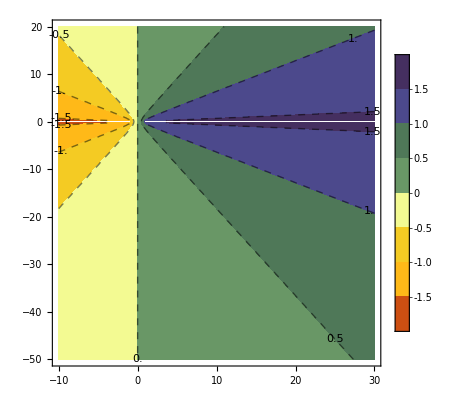

```mathematica
ContourPlot[
Re[ArcSin[z]], 
{x,-10,30},{y,-50,20}, 
PlotLegends->Automatic,
ContourLabels->True,
ContourShading->ColorData[35,"ColorList"],
ContourStyle->Dashed,
ImageSize->Full]
```

```mathematica
,
```